Info on the notebook:
This notebook uses the BiGONLight package to compute observables in conformal EdS model.
It is structured as follows: 
- model set-up:  give the 4D metric tensor components as input and compute the 3+1 quantities lapse α, shift β^i, spatial metric γ_ij, extrinsic curvature K_ij and the normal vector n^μ;
- geodesic: provide initial position and tangent vector {x^μ, ℓ^μ} as input to find null geodesics;
- parallel transported frame: give the initial conditions for a frame (ϕ^μ)_αthat will be parallel transported along the computed geodesic (we use the SNF, i.e. (ϕ^μ)_α={u^μ,(ϕ^μ)_1,(ϕ^μ)_2, ℓ^μ} with u^μ the four-velocity and (ϕ^μ)_A two orthonormal vectors)
- optical tidal matrix: compute the optical tidal matrix (R^μ)_ρσν ℓ^ρ ℓ^σ in the parallel propagated frame; 
- BGO: compute and solve the Geodesic Deviation Equation for the Bi-local Geodesic Operators along the null geodesic;
- observables: compute the optical observables in the BGO framework: redshift, redshift drift, angular diameter distance, luminosity distance, parallax distance, distance slip, convergence and shear.

Set the current directory as working directory and load the package.

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["bigonlight`"]
$PreRead=(#/.s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>s<>"`70."&);
```

a generic direction can be written as 𝓋^μ=𝓋^0∂_0 +Γ(sinχ cosξ ∂_1 +sinχ sinξ ∂_1 +cosχ ∂_3)=(𝓋^0(∂_0))^μ+Γ (N⃗)^μ with respect to the local tetrad ∂_μ . 
In particular for a null direction 𝓋^0=±1 and Γ=1 , while for a timelike direction 𝓋^0=±c Γ and ψ=c Γ β  where β=vel/c the normalized velocity and Γ=1/(√(1-β^2)) the Lorentz factor.
import data on files
BGO=<<”BGO_data.m”;
totN=<<”geodesic_data.m”;

```mathematica
𝒱[Vt_,lorentz_,direction1_,direction2_]:=
Module[{V0=Vt, γ=lorentz,χ=direction1,ξ=direction2},
V0{1,0,0,0}+γ(Sin[χ]Cos[ξ]{0,1,0,0}+Sin[χ]Sin[ξ]{0,0,1,0}+Cos[χ]{0,0,0,1})
]

StandardPlotStyle[size_,sizelegend_,ylabel_,xlabel_,title_,legend_,position_]:=Module[{ft=size,ftL=sizelegend,yL=ylabel,xL=xlabel,pt=title,list=legend,pl=position},
If[ list=={},{FrameLabel->{{yL,""},{xL,""}},Frame->True,FrameTicks->True,FrameStyle->Directive[FontSize->ft],GridLines->Automatic,GridLinesStyle->Directive[Gray,Opacity[0.2],Dashed],PlotLabel->Style[pt,Bold,FontSize->ft]},{FrameLabel->{{yL,""},{xL,""}},Frame->True,FrameTicks->True,FrameStyle->Directive[FontSize->ft],GridLines->Automatic,GridLinesStyle->Directive[Gray,Opacity[0.2],Dashed],PlotLabel->Style[pt,Bold,FontSize->ft],PlotLegends->Placed[LineLegend[Table[Style[list[[m]],FontSize->ftL],{m,1,Length[list]}]],pl]},Print["Error"]]];
```

```mathematica
1+2+3+...+x+(x+1)+(x+2)+..+n/2+...+(n-(x+2))+(n-(x+1))+(n-x)+...+(n-2)+(n-1)+n
(n(n+1))/2=S

((n-6)(n+1))/2+(n-(x+2))+(n-(x+1))+(n-x)=S
```

55

55

# Conformal time EdS

In this notebook we use geometric units G=c=1. This allows us to express mass, length and  time as the same unit. For our convenience, we will express all quantities as dimension-less quantities in units of length L. Therefore, any physical quantity Q^phys=Q^comp L^α where α is a certain exponent and Q^comp is dimensionless. 
L is arbitrary chosen: in particular, we choose to set L such that ℋ_0 L=2 (from Friedman equations, such that η_0==1).
In units of Mpc, we have L=2/ℋ_0=2/(67.36/299792.458[km/(s Mpc) 1/(km/s)])=8901.2 Mpc.
The computational present time is η_0^comp==η_0/L==1

## Units and Parameters

```mathematica
(da/(a Sqrt[(Ωm0/a+ΩΛ a^2)]))= Subscript[H, 0] dt
```

```mathematica
L=2/(H0 Sqrt[Ωm0])/.{H0->67.36/299792.458, Ωm0->1}(*Mpc*);

𝒽0=2/Sqrt[Ωm0]/.{ Ωm0->1};
ETA0=1;
ηin=2/(𝒽0 Sqrt[Ωm0])Sqrt[1/11]/.{ Ωm0->1};
```

```mathematica
L
```

8901.2

```mathematica
param={Ωm0->1, c->1};
```

## Model set-up

We need to provide the spacetime metric g_μν. 
This can be done in two ways: 
		1)  writing the analytic expression for the metric components g_μν=(g_00 | g_01 | g_02 | g_03
g_10 | g_11 | g_12 | g_13
g_20 | g_21 | g_22 | g_23
g_30 | g_31 | g_32 | g_33) 
		2) import data from a (relativistic) numerical simulation. 
		
In this case, we know the form of the metric g_μν, so we use the first method.

```mathematica
Clear[A,𝒟,ϕ,ℋ]
```

```mathematica
Clear[α,β,g,K,g4,X,V,e,Energy,nd,nu,x,y,z,η]
```

```mathematica
X4={η,x,y,z};
X={x,y,z};
V={v1,v2,v3};
e={e1,e2,e3};
Energy={energy, λ};
```

```mathematica
g4={{-(A[η])^2,0,0,0},{0,(A[η])^2,0,0},{0,0,(A[η])^2,0},{0,0,0,(A[η])^2}};
```

```mathematica
?ADM
```

```mathematica
solADM=ADM[g4,X4];
α=Evaluate[solADM[[1]]]
β=Evaluate[solADM[[2]]]
g=Evaluate[solADM[[3]]]
K=Evaluate[solADM[[4]]]
nu=Evaluate[solADM[[5]]]
nd=Evaluate[solADM[[6]]]
```

√(η^4)

{0,0,0}

{{η^4,0,0},{0,η^4,0},{0,0,η^4}}

{{-(2 √(η^4))/η,0,0},{0,-(2 √(η^4))/η,0},{0,0,-(2 √(η^4))/η}}

{1/(√(η^4)),0,0,0}

{-√(η^4),0,0,0}

```mathematica
αα[τ_]:=α/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
ββ[τ_]:=β/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
VV[η_]:=Table[V[[i]][η],{i,1,Length[X]}];
gg[τ_]:=g/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
gg4[τ_]:=g4/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
nup[τ_]:=nu/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
ndown[τ_]:=nd/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];

αlup[η_]:=(*EBG[η]*)αα[η] (nup[η]+Flatten[{0,VV[η]}]);
αldown[η_]:=(*EBG[η]*)αα[η](ndown[η]+Flatten[{0,gg[η].VV[η]}]);
```

## Geodesic

```mathematica
?GeodesicEquations
?EnergyEquations
```

```mathematica
geodBG=GeodesicEquations[X,V,g,K,α,β,η]
```

{x'[η]==√(η^4) v1[η],v1'[η]==√(η^4) (-(4 √(η^4) v1[η])/η^5+v1[η] ((2 √(η^4) v1[η]^2)/η+(2 √(η^4) v2[η]^2)/η+(2 √(η^4) v3[η]^2)/η)),y'[η]==√(η^4) v2[η],v2'[η]==√(η^4) (-(4 √(η^4) v2[η])/η^5+v2[η] ((2 √(η^4) v1[η]^2)/η+(2 √(η^4) v2[η]^2)/η+(2 √(η^4) v3[η]^2)/η)),z'[η]==√(η^4) v3[η],v3'[η]==√(η^4) (-(4 √(η^4) v3[η])/η^5+v3[η] ((2 √(η^4) v1[η]^2)/η+(2 √(η^4) v2[η]^2)/η+(2 √(η^4) v3[η]^2)/η))}

```mathematica
enereqBG=EnergyEquations[g,K,α,β,Energy,X,V,η]
```

{energy'[η]==√(η^4) energy[η] (-(2 √(η^4) v1[η]^2)/η-(2 √(η^4) v2[η]^2)/η-(2 √(η^4) v3[η]^2)/η),λ'[η]==(√(η^4))/energy[η]}

```mathematica
A[η_]:=((𝒽0^2 Ωm0)/4 η^2)/.param;
ℋ[η_]:=(𝒽0) Sqrt[Ωm0/A[η]]/.param;(*(𝒽0/L) Sqrt[Ωm0/A[η]+ΩΛ A[η]^2]/.param;*)
```

### Initial conditions

The initial conditions can be given in two different ways:
1) directly specifying the values or
2) giving the initial direction v^2 and v^3 and use the function InitialConditions[] to compute v^1 such that the geodesic is null.
Here we set the initial tangent vector as  ℓ^μ=(𝓋^0(∂_0))^μ+Γ (N⃗)^μ which is null with the choice 𝓋^0==-1 and Γ ==1 for any direction (N⃗)^μand we perform the 3+1 splitting with Vsplit[].
 Then we check that is actually null by using the InitialConditions[] function

```mathematica
κ=SetPrecision[𝒱[-1,1,π/4,π/4],70]
```

{-1.,0.5,0.5,0.7071067811865475244008443621048490392848359376884740365883398689953662}

```mathematica
?Vsplit
```

The vector κ^μ must be expressed in 3+1 form κ^μ=E(n^μ+V^μ) where E=-κ^μ n_μ and V^μ=κ^μ/E-n^μ

```mathematica
ℓsplit=Vsplit[κ,nup[ETA0],ndown[ETA0]];
```

3+1 Initial conditions

```mathematica
substitution={η->ETA0,x->0,y->0,z->0,v2->ℓsplit[[2,2]],v3->ℓsplit[[2,3]]};
```

```mathematica
?InitialConditions
```

```mathematica
initialvel1=Flatten[InitialConditions[g,substitution,V,param]]
initialBG=(*{x[ETA0]==0,y[ETA0]==0,v2[ETA0]==0,z[ETA0]==0,v3[ETA0]==0,v1[1]==-1}*)Flatten[Join[Table[(substitution[[i,1]][η]/.substitution[[1]])==substitution[[i,2]],{i,2,Length[substitution]}],{(V[[1]][η]/.substitution[[1]])==initialvel1[[2,2]](*-2.5 10^-4*)(*(V[[1]]/.initialvel1[[2]])*)}]]
E0BG=ℓsplit[[1]](*α/.η->ηin*)(*ϵ*)
initialenergy={Energy[[1]][ETA0]==E0BG,Energy[[2]][ETA0]==1}
```

{v1→-0.5,v1→0.5}

{x[1]==0,y[1]==0,z[1]==0,v2[1]==-0.5,v3[1]==-0.70710678118654752440084436210484903928483593768847,v1[1]==0.5}

-1.

{energy[1]==-1.,λ[1]==1}

### Solve the equations numerically, given the functions in the metric explicitly

```mathematica
?SolveGeodesic
?SolveEnergy
```

```mathematica
AbsoluteTiming[solgeodesic=Flatten[SolveGeodesic[geodBG,initialBG,X,V,param,η,ηin,ETA0,"SS",60,60,10,5]]]
```

NDSolve::precw: The precision of the differential equation ({{x'[η]==√(η^4) v1[η],v1'[η]==√(η^4) (-(4 √Power[«2»] v1[η])/η^5+v1[η] (Times[«4»]+Times[«4»]+Times[«4»])),y'[η]==√(η^4) v2[η],v2'[η]==√(η^4) (-(4 √Power[«2»] v2[η])/η^5+v2[η] (Times[«4»]+Times[«4»]+Times[«4»])),«4»,z[1]==0,v2[1]==-0.5,v3[1]==-0.70710678118654752440084436210484903928483593768847,v1[1]==0.5},{},{},{},{}}) is less than WorkingPrecision (50.).

{2.04317,{x→InterpolatingFunction[…],y→InterpolatingFunction[…],z→InterpolatingFunction[…],v1→InterpolatingFunction[…],v2→InterpolatingFunction[…],v3→InterpolatingFunction[…]}}

```mathematica
AbsoluteTiming[solenergy=Flatten[SolveEnergy[enereqBG,initialenergy,Energy,solgeodesic,param,η,ηin,ETA0,"SS",50,50,10,5]]]
```

{1.77325,{energy→InterpolatingFunction[…],λ→InterpolatingFunction[…]}}

Test that the constraint conditions are satisfied for all the evolution

```mathematica
geodesic=Join[solgeodesic,solenergy];
```

Note: 	the solution can be saved in a file as: geodesic >> “file_name.m”.
		Similarly, “.m” files can be imported using the syntax:  geodesic =<<”file_name.m”

```mathematica
geodesic=<<"EdS_geodesic_bisect.m";
```

Test the null condition along the geodesic

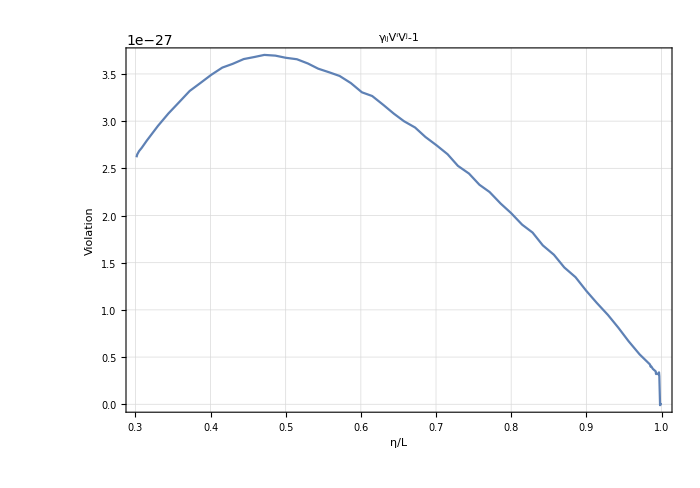

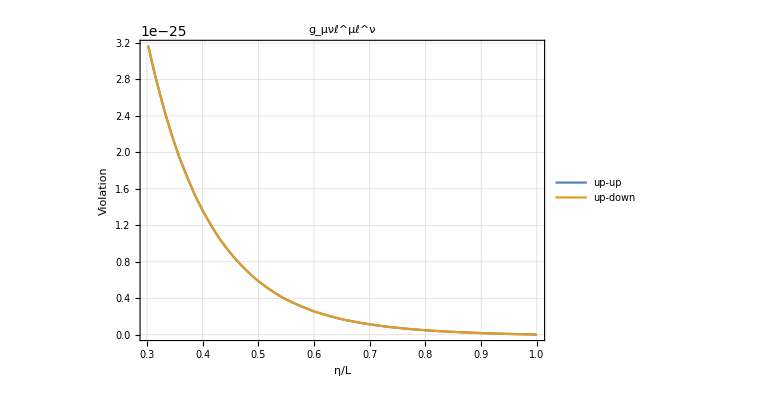

```mathematica
EBG[η_]:=energy[η]/.geodesic;
lup[η_]:=EBG[η](nup[η]+Flatten[{0,VV[η]}]);
ldown[η_]:=EBG[η](ndown[η]+Flatten[{0,gg[η].VV[η]}]);
Plot[Evaluate[{gg[η].VV[η].VV[η]-1}/.geodesic/.param], {η, ηin,ETA0},PlotRange->All,WorkingPrecision->60,AspectRatio->0.7,ImageSize->700,Evaluate[StandardPlotStyle[16,24,"Violation","η/L","γ_ijV^iV^j-1",{},{}]]]
Plot[Evaluate[{gg4[η].lup[η].lup[η],lup[η].ldown[η]}/.geodesic/.param], {η, ηin,ETA0},PlotRange->Full,WorkingPrecision->60,AspectRatio->0.7,ImageSize->Large,Evaluate[StandardPlotStyle[16,24,"Violation","η/L","g_μνℓ^μℓ^ν",{"up-up","up-down"},{0.6,0.6}]]]
```

```mathematica
geodesic>>"EdS_geodesic_bisect.m"
```

### Compute the redshift

The  redshift is defined as z+1==(g_μν u^μ ℓ^ν|_𝒮)/(g_μν u^μ ℓ^ν|_𝒪). 
In 3+1, decomposing u^μ==Γ(n^μ+U^μ) and ℓ^μ=ℰ(n^μ+V^μ), the redshift becomes: z+1==ℰ_𝒮/ℰ_𝒪(1-γ_ij V^i U^j|_𝒮)/(1-γ_ij V^i U^j|_𝒪)((1-γ_ij U^i U^j|_𝒮)/(1-γ_ij U^i U^j|_𝒪))^(1/2). In synchronous-comoving coordinates U^i==0 and the redshift simplifies to z+1==ℰ_𝒮/ℰ_𝒪

```mathematica
redshift[η_]:=EBG[η]/EBG[ETA0]-1(*A[ETA0]/A[η]-1*)
zan[η_]:=A[ETA0]/A[η]-1;
```

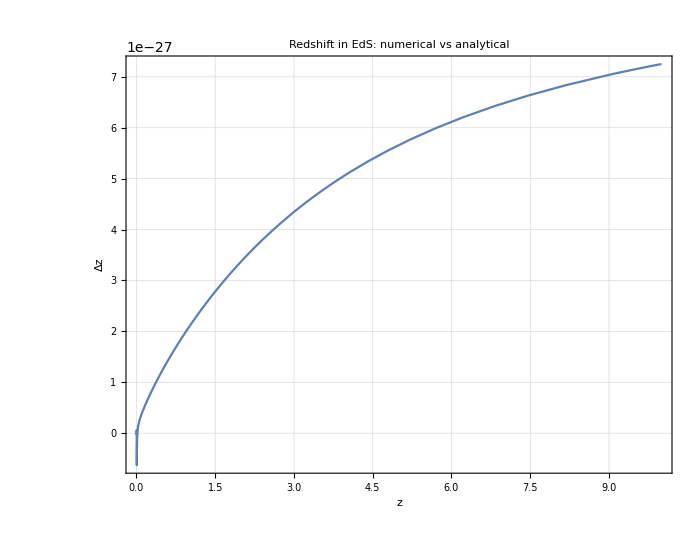

```mathematica
ParametricPlot[{redshift[η], Evaluate[ redshift[η]/zan[η]-1]},{η,ηin,ETA0},WorkingPrecision->40,ImageSize->700,AspectRatio->0.8,PlotRange->All,Evaluate[StandardPlotStyle[18,24,"Δz","z","Redshift in EdS: numerical vs analytical ",{},{}]]]
```

Compute the null geodesic

```mathematica
trajectoryBG[η_]:=Flatten[{x[η] ,y[η] ,z[η] }/.geodesic/.param];
Show[ParametricPlot3D[trajectoryBG[η],{η,ηin,ETA0},PlotRange->{{-1,1},{-1,1},{-1,1}}, ImageSize->700, ViewPoint->{0,0,Infinity}, AxesLabel->{"X/L","Y/L","Z/L"}]/.Line[x_]:>Sequence[Arrowheads[Table[.02,{100}]],Arrow@Line[x]] ]
```

-Graphics3D-

## Parallel transport of a frame

```mathematica
Clear[transport2,vecbcframe,soltrans2,soldeviation,solGDE,tot1,tot2,totl,totu,Cu,Cl,Cf1,Cf2,Pu,Pl,P1,P2,F,F0,EE,EE0,OPT,ξ,ξA,ξbc,Ξ,ξ4,DA,DAbc,DAsolGDE,JMAP,frame,frame0]
```

```mathematica
frame0={fu0,f10,f20,fl0};
frame={{fu1,fu2,fu3},{f11,f12,f13},{f21,f22,f23},{fl1,fl2,fl3}};
```

### set-up the initial conditions for the SNF

Here we can set up the initial condition for doing the parallel transport of the SNF (ϕ^μ)_α. This can be done by giving the vectors of the frame in 3+1 components in the form (ϕ^μ)_α=Φ_α n^μ+(F^μ)_α , with Φ_α and (F^μ)_α the normal and the tangent part respectively. 
Alternatively, the user can provide the initial: 
	- the  four-velocity u^μ, 
	- the tangent vector ℓ^μ,
	- two directions for the orthonormal vectors p_1^μ and p_2^μ .
and use  SNF[] to find the SNF in 3+1. The SNF[] function uses the two directions p_1^μ and p_2^μ to compute the orthonormal ϕ_1^μ and ϕ_2^μ according to the SNF relations. Then it performs the 3+1 of all the four vectors in a form ready to be used as initial conditions for PTransportedFrame[].

The four-velocity u^μ ( and eventually the four-acceleration w^μ) of the observer (or source) is  the other input. In this case, we are in synchronous-comoving gauge and it is simply u^μ=(1/a,0,0,0). If needed it

```mathematica
(*U={0,0,0};
Γl=Sqrt[1/(1-γ.U.U)]
uu=Γl(nup[η]+Join[{0},U])*)
u[η_]:=SetPrecision[{1/A[η],0,0,0},50]
u[ETA0]//N
u[ηin]//N
```

{1.,0.,0.,0.}

{11.,0.,0.,0.}

```mathematica
gg4[ηin].u[ηin].lup[ηin]/.Join[geodesic,param]
gg4[η].u[η].u[η](*/.Join[exactgeodesicBG,param]*)
```

11.00000000000000000000000007251113047895202540243

-1

```mathematica
?SNF
```

```mathematica
p1={0,0,1,0};
p2={0,0,0,1};
```

```mathematica
snfSplit=SNF[gg4[ETA0],u[ETA0],lup[ETA0]/.geodesic,p1,p2,nup[ETA0],ndown[ETA0]]-snfSplit
```

### Parallel transport the SNF

```mathematica
initialframeBG=Table[Flatten[{frame0[[i]][ETA0]==snfSplit[[i,1]],Table[frame[[i,j]][ETA0]==snfSplit[[i,2]][[j]],{j,1,3}]}],{i,1,4}];
```

```mathematica
?PTransportedFrame
```

```mathematica
Timing[soltransBG=Flatten[PTransportedFrame[g,K,α,β,geodesic,initialframeBG,frame,frame0,param,η,ηin,ETA0,"SS",60,60,10,5]]]
```

{12.8398,{fu1→InterpolatingFunction[{{0.30151134457776362264681206697006242581155350414449, 1.0000000000000000000000000000000000000000000000000}}, <>],fu2→InterpolatingFunction[{{0.30151134457776362264681206697006242581155350414449, 1.0000000000000000000000000000000000000000000000000}}, <>],fu3→InterpolatingFunction[{{0.30151134457776362264681206697006242581155350414449, 1.0000000000000000000000000000000000000000000000000}}, <>],fu0→InterpolatingFunction[{{0.30151134457776362264681206697006242581155350414449, 1.0000000000000000000000000000000000000000000000000}}, <>],f11→InterpolatingFunction[…],f12→InterpolatingFunction[…],f13→InterpolatingFunction[…],f10→InterpolatingFunction[…],f21→InterpolatingFunction[…],f22→InterpolatingFunction[…],f23→InterpolatingFunction[…],f20→InterpolatingFunction[…],fl1→InterpolatingFunction[{{0.30151134457776362264681206697006242581155350414449, 1.0000000000000000000000000000000000000000000000000}}, <>],fl2→InterpolatingFunction[{{0.30151134457776362264681206697006242581155350414449, 1.0000000000000000000000000000000000000000000000000}}, <>],fl3→InterpolatingFunction[{{0.30151134457776362264681206697006242581155350414449, 1.0000000000000000000000000000000000000000000000000}}, <>],fl0→InterpolatingFunction[{{0.30151134457776362264681206697006242581155350414449, 1.0000000000000000000000000000000000000000000000000}}, <>]}}

```mathematica
totBG=Flatten[Join[Flatten[soltransBG],geodesic]];
```

```mathematica
totBG=<<"EdS_ptSNF_bisect.m";
```

```mathematica
Cu[η_]:=fu0[η];
Cf1[η_]:=f10[η];
Cf2[η_]:=f20[η];
Cl[η_]:=fl0[η];
Pu[η_]:={fu1[η],fu2[η],fu3[η]};
P1[η_]:={f11[η],f12[η],f13[η]};
P2[η_]:={f21[η],f22[η],f23[η]};
Pl[η_]:={fl1[η],fl2[η],fl3[η]};
```

```mathematica
Show[ParametricPlot3D[trajectoryBG[η],{η,ηin,ETA0},PlotRange->{{-2,2},{-2,2},{-2,2}}]/.Line[x_]:>Sequence[Arrowheads[Table[.02,{100/10}]],Arrow@Line[x]] ,Graphics3D[{{Red,Arrowheads[0.02],Table[Arrow[{trajectoryBG[η],(trajectoryBG[η]+(Pu[η]/.totBG))}],{η,ηin,ETA0,0.05}]},{Green,Arrowheads[0.02],Table[Arrow[{trajectoryBG[η],(trajectoryBG[η]+(P1[η]/.totBG))}],{η,ηin,ETA0,0.05}]},{Blue,Arrowheads[0.02],Table[Arrow[{trajectoryBG[η],(trajectoryBG[η]+(P2[η]/.totBG))}],{η,ηin,ETA0,0.05}]},{Black,Arrowheads[0.02],Table[Arrow[{trajectoryBG[η],(trajectoryBG[η]+(Pl[η]/.totBG))}],{η,ηin,ETA0,0.05}]}}],Graphics3D[Sphere[{0,0,0},0.05]] , ImageSize->700,ViewPoint->{0,100,10},AxesLabel->{x,y,z},AxesStyle->Directive[Red,12]]
```

-Graphics3D-

### Define the induced metric of the SNF “h”

```mathematica
Clear[F,F0,EE,EE0,Q,h]
```

```mathematica
Q=Re[((gg4[ETA0].(Evaluate[Cu[ETA0]nup[ETA0]+Flatten[{0, Pu[ETA0]}]]).(Evaluate[Cl[ETA0]nup[ETA0]+Flatten[{0, Pl[ETA0]}]]))/.totBG/.param)];
h={{-1,0,0,Q},{0,1,0,0},{0,0,1,0},{Q,0,0,0}};
Ih=Inverse[h];
```

```mathematica
F[t_]:={{Pu[t][[1]],P1[t][[1]],P2[t][[1]],Pl[t][[1]]},{Pu[t][[2]],P1[t][[2]],P2[t][[2]],Pl[t][[2]]},{Pu[t][[3]],P1[t][[3]],P2[t][[3]],Pl[t][[3]]}};
F0[t_]:={Cu[t],Cf1[t],Cf2[t],Cl[t]};
```

```mathematica
totBG>>"EdS_ptSNF_bisect.m"
```

#### Check SNF

-0.57735026630287451474075727918495279118

```mathematica
(gg4[t].u[t].s1)/.Join[geodesic,param]/.t->ETA0
(gg4[t].u[t].s2)/.Join[geodesic,param]/.t->ETA0
(gg4[t].lup[t].s1)/.Join[geodesic,param]/.t->ETA0
(gg4[t].lup[t].s2)/.Join[geodesic,param]/.t->ETA0
(gg4[t].s1.s2)/.Join[geodesic,param]/.t->ETA0
(gg4[t].s1.s1)/.Join[geodesic,param]/.t->ETA0
(gg4[t].s2.s2)/.Join[geodesic,param]/.t->ETA0
(gg4[t].lup[t].u[t])/.Join[geodesic,param]/.t->ETA0
(gg4[t].u[t].u[t])/.Join[geodesic,param]/.t->ETA0
(gg4[t].lup[t].lup[t])/.Join[geodesic,param]/.t->ETA0
```

0.

0.

0.

«2 more identical outputs»

1.

1.

1.

-1

0.

```mathematica
Check of the relations: u^μ Subscript[u, μ]=-1,f1^μ Subscript[f1, μ]=1,f2^μ Subscript[f2, μ]=1,k^μ Subscript[k, μ]=0
```

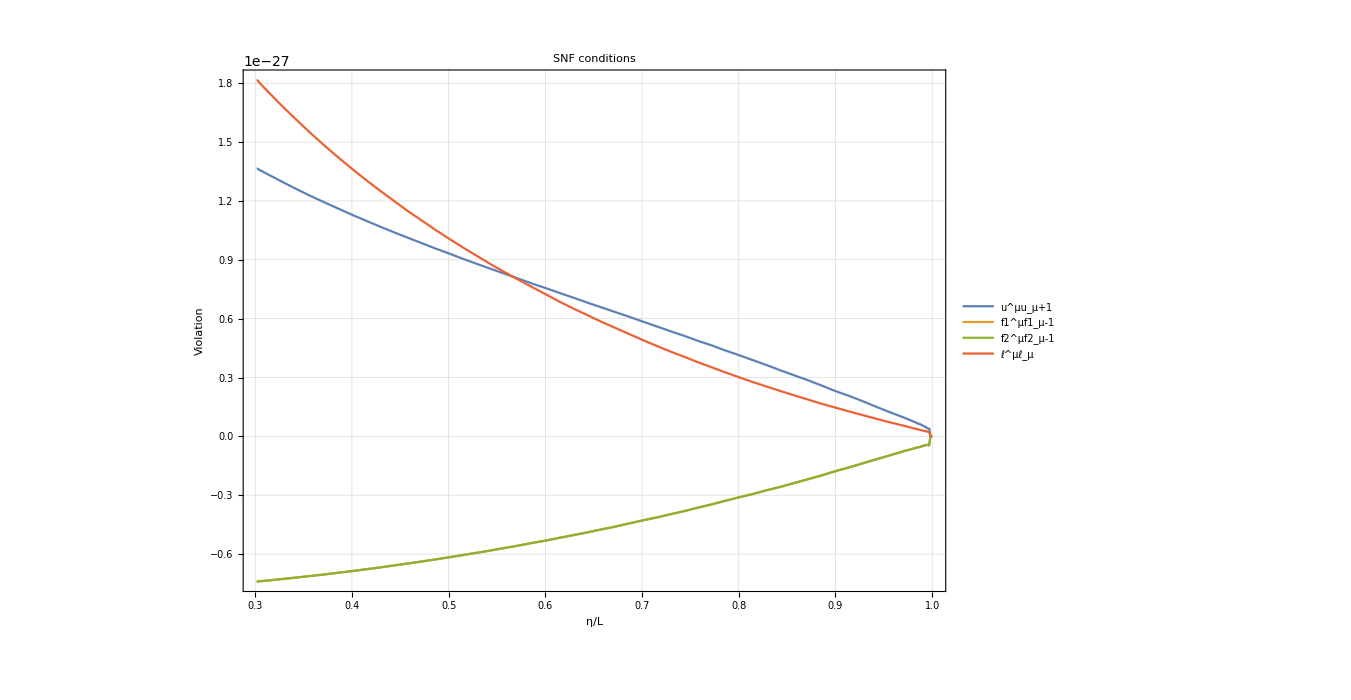

```mathematica
Plot[{(gg4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]).(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]])+1)/.totBG/.param,(gg4[η].(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]).(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]])-1)/.totBG/.param,(gg4[η].(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]])-1)/.totBG/.param,(gg4[η].(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]).(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]))/.totBG/.param},{η,ηin,ETA0},PlotRange->All,WorkingPrecision->60,AspectRatio->0.7,ImageSize->1000,Evaluate[StandardPlotStyle[16,24,"Violation","η/L","SNF conditions",{"u^μu_μ+1","f1^μf1_μ-1","f2^μf2_μ-1","ℓ^μℓ_μ"},{0.8,0.8}]]]
```

```mathematica
Check of the relations: u^μ Subscript[f1, μ]=0,u^μ Subscript[f2, μ]=0,k^μ Subscript[f1, μ]=0,k^μ Subscript[f2, μ]=0
```

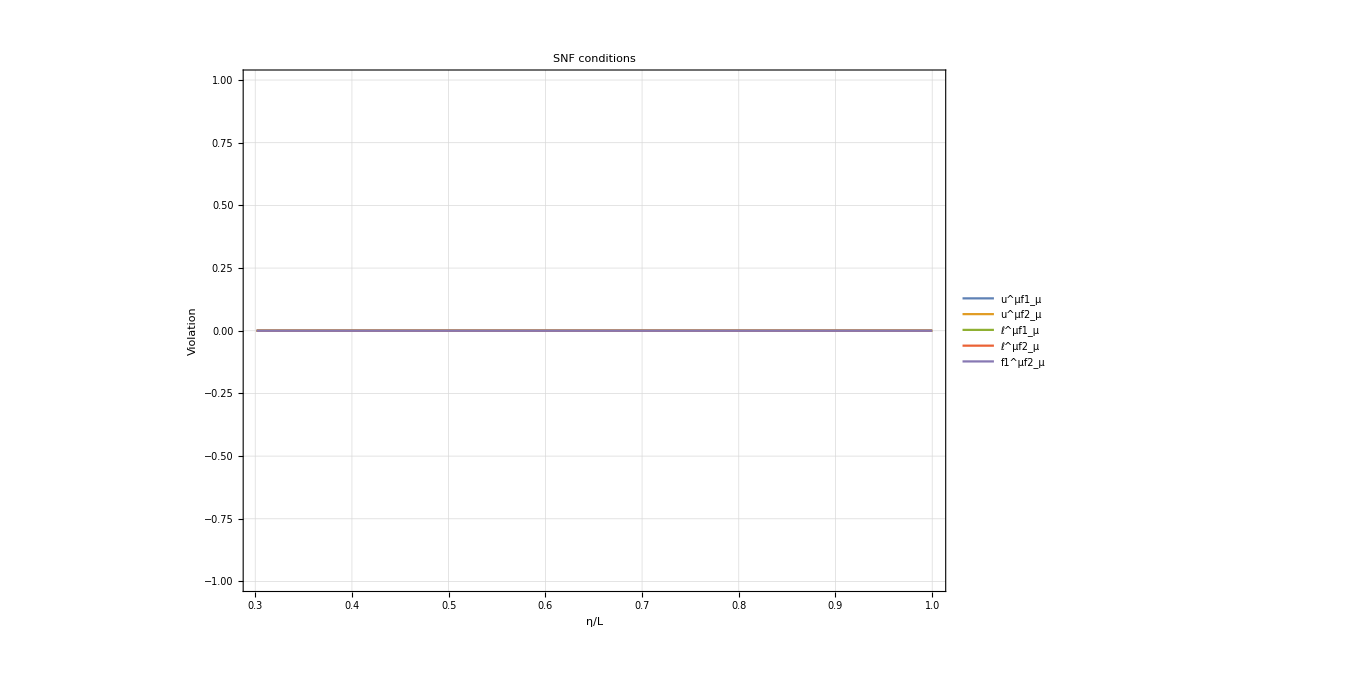

```mathematica
Plot[{(gg4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]).(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]))/.totBG/.param,(gg4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]))/.totBG/.param,(gg4[η].(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]).(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]))/.totBG/.param,(gg4[η].(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]))/.totBG/.param,(gg4[η].(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]))/.totBG/.param},{η,ηin,ETA0},PlotRange->All,WorkingPrecision->60,AspectRatio->0.7,ImageSize->1000,Evaluate[StandardPlotStyle[16,24,"Violation","η/L","SNF conditions",{"u^μf1_μ","u^μf2_μ","ℓ^μf1_μ","ℓ^μf2_μ","f1^μf2_μ"},{0.8,0.3}]]]
```

```mathematica
NQ[η_]:=(gg4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]).(*lup[η]*)(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]])/.totBG/.param)
```

```mathematica
lup[ETA0][[1]]
```

-1.

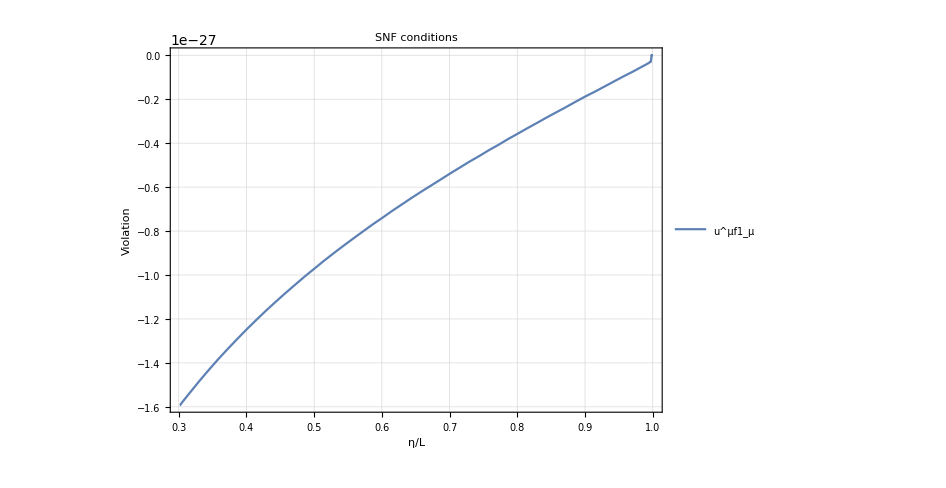

```mathematica
Plot[Evaluate[NQ[η]-(-lup[ETA0][[1]])],{η,ηin,ETA0},PlotRange->All,WorkingPrecision->Precision[lup[ETA0][[1]]],AspectRatio->0.7,ImageSize->700,Evaluate[StandardPlotStyle[16,24,"Violation","η/L","SNF conditions",{"u^μf1_μ","ℓ^μf1_μ"},{0.8,0.3}]]]
```

## Optical Tidal Matrix

```mathematica
Clear[A,𝒟,ϕ,ℋ]
```

```mathematica
?OpticalTidalMatrix
```

```mathematica
Timing[OPT=OpticalTidalMatrix[X,V,frame,frame0,Q,g,K,α,β,η]//Simplify;]
```

{0.661224,Null}

```mathematica
OPT//MatrixForm
```

(0 | 0 | 0 | 0
-f12[η] fu2[η] v1[η]^2 A'[η]^2-f13[η] fu3[η] v1[η]^2 A'[η]^2+f12[η] fu1[η] v1[η] v2[η] A'[η]^2+f11[η] fu2[η] v1[η] v2[η] A'[η]^2-f11[η] fu1[η] v2[η]^2 A'[η]^2-f13[η] fu3[η] v2[η]^2 A'[η]^2+f13[η] fu1[η] v1[η] v3[η] A'[η]^2+f11[η] fu3[η] v1[η] v3[η] A'[η]^2+f13[η] fu2[η] v2[η] v3[η] A'[η]^2+f12[η] fu3[η] v2[η] v3[η] A'[η]^2-f11[η] fu1[η] v3[η]^2 A'[η]^2-f12[η] fu2[η] v3[η]^2 A'[η]^2+((f13[η] fu3[η]-f10[η] fu1[η] v1[η]+f10[η] fu0[η] v1[η]^2+f11[η] (fu1[η]-fu0[η] v1[η])-f10[η] fu2[η] v2[η]+f10[η] fu0[η] v2[η]^2+f12[η] (fu2[η]-fu0[η] v2[η])-f13[η] fu0[η] v3[η]-f10[η] fu3[η] v3[η]+f10[η] fu0[η] v3[η]^2) (-A'[η]^2+A[η] A''[η]))/A[η]^2 | (-(f11[η]^2+f12[η]^2+f13[η]^2-2 f10[η] f11[η] v1[η]+f10[η]^2 v1[η]^2-2 f10[η] f12[η] v2[η]+f10[η]^2 v2[η]^2-2 f10[η] f13[η] v3[η]+f10[η]^2 v3[η]^2+A[η]^2 (f13[η]^2 (v1[η]^2+v2[η]^2)-2 f11[η] f13[η] v1[η] v3[η]-2 f12[η] v2[η] (f11[η] v1[η]+f13[η] v3[η])+f12[η]^2 (v1[η]^2+v3[η]^2)+f11[η]^2 (v2[η]^2+v3[η]^2))) A'[η]^2+A[η] (f11[η]^2+f12[η]^2+f13[η]^2-2 f10[η] f11[η] v1[η]+f10[η]^2 v1[η]^2-2 f10[η] f12[η] v2[η]+f10[η]^2 v2[η]^2-2 f10[η] f13[η] v3[η]+f10[η]^2 v3[η]^2) A''[η])/A[η]^2 | -f12[η] f22[η] v1[η]^2 A'[η]^2-f13[η] f23[η] v1[η]^2 A'[η]^2+f12[η] f21[η] v1[η] v2[η] A'[η]^2+f11[η] f22[η] v1[η] v2[η] A'[η]^2-f11[η] f21[η] v2[η]^2 A'[η]^2-f13[η] f23[η] v2[η]^2 A'[η]^2+f13[η] f21[η] v1[η] v3[η] A'[η]^2+f11[η] f23[η] v1[η] v3[η] A'[η]^2+f13[η] f22[η] v2[η] v3[η] A'[η]^2+f12[η] f23[η] v2[η] v3[η] A'[η]^2-f11[η] f21[η] v3[η]^2 A'[η]^2-f12[η] f22[η] v3[η]^2 A'[η]^2+((f13[η] f23[η]-f10[η] f21[η] v1[η]+f10[η] f20[η] v1[η]^2+f11[η] (f21[η]-f20[η] v1[η])-f10[η] f22[η] v2[η]+f10[η] f20[η] v2[η]^2+f12[η] (f22[η]-f20[η] v2[η])-f13[η] f20[η] v3[η]-f10[η] f23[η] v3[η]+f10[η] f20[η] v3[η]^2) (-A'[η]^2+A[η] A''[η]))/A[η]^2 | 0
-f22[η] fu2[η] v1[η]^2 A'[η]^2-f23[η] fu3[η] v1[η]^2 A'[η]^2+f22[η] fu1[η] v1[η] v2[η] A'[η]^2+f21[η] fu2[η] v1[η] v2[η] A'[η]^2-f21[η] fu1[η] v2[η]^2 A'[η]^2-f23[η] fu3[η] v2[η]^2 A'[η]^2+f23[η] fu1[η] v1[η] v3[η] A'[η]^2+f21[η] fu3[η] v1[η] v3[η] A'[η]^2+f23[η] fu2[η] v2[η] v3[η] A'[η]^2+f22[η] fu3[η] v2[η] v3[η] A'[η]^2-f21[η] fu1[η] v3[η]^2 A'[η]^2-f22[η] fu2[η] v3[η]^2 A'[η]^2+((f23[η] fu3[η]-f20[η] fu1[η] v1[η]+f20[η] fu0[η] v1[η]^2+f21[η] (fu1[η]-fu0[η] v1[η])-f20[η] fu2[η] v2[η]+f20[η] fu0[η] v2[η]^2+f22[η] (fu2[η]-fu0[η] v2[η])-f23[η] fu0[η] v3[η]-f20[η] fu3[η] v3[η]+f20[η] fu0[η] v3[η]^2) (-A'[η]^2+A[η] A''[η]))/A[η]^2 | -f12[η] f22[η] v1[η]^2 A'[η]^2-f13[η] f23[η] v1[η]^2 A'[η]^2+f12[η] f21[η] v1[η] v2[η] A'[η]^2+f11[η] f22[η] v1[η] v2[η] A'[η]^2-f11[η] f21[η] v2[η]^2 A'[η]^2-f13[η] f23[η] v2[η]^2 A'[η]^2+f13[η] f21[η] v1[η] v3[η] A'[η]^2+f11[η] f23[η] v1[η] v3[η] A'[η]^2+f13[η] f22[η] v2[η] v3[η] A'[η]^2+f12[η] f23[η] v2[η] v3[η] A'[η]^2-f11[η] f21[η] v3[η]^2 A'[η]^2-f12[η] f22[η] v3[η]^2 A'[η]^2+((f13[η] f23[η]-f10[η] f21[η] v1[η]+f10[η] f20[η] v1[η]^2+f11[η] (f21[η]-f20[η] v1[η])-f10[η] f22[η] v2[η]+f10[η] f20[η] v2[η]^2+f12[η] (f22[η]-f20[η] v2[η])-f13[η] f20[η] v3[η]-f10[η] f23[η] v3[η]+f10[η] f20[η] v3[η]^2) (-A'[η]^2+A[η] A''[η]))/A[η]^2 | (-(f21[η]^2+f22[η]^2+f23[η]^2-2 f20[η] f21[η] v1[η]+f20[η]^2 v1[η]^2-2 f20[η] f22[η] v2[η]+f20[η]^2 v2[η]^2-2 f20[η] f23[η] v3[η]+f20[η]^2 v3[η]^2+A[η]^2 (f23[η]^2 (v1[η]^2+v2[η]^2)-2 f21[η] f23[η] v1[η] v3[η]-2 f22[η] v2[η] (f21[η] v1[η]+f23[η] v3[η])+f22[η]^2 (v1[η]^2+v3[η]^2)+f21[η]^2 (v2[η]^2+v3[η]^2))) A'[η]^2+A[η] (f21[η]^2+f22[η]^2+f23[η]^2-2 f20[η] f21[η] v1[η]+f20[η]^2 v1[η]^2-2 f20[η] f22[η] v2[η]+f20[η]^2 v2[η]^2-2 f20[η] f23[η] v3[η]+f20[η]^2 v3[η]^2) A''[η])/A[η]^2 | 0
(1. (-(fu1[η]^2+fu2[η]^2+fu3[η]^2-2 fu0[η] fu1[η] v1[η]+fu0[η]^2 v1[η]^2-2 fu0[η] fu2[η] v2[η]+fu0[η]^2 v2[η]^2-2 fu0[η] fu3[η] v3[η]+fu0[η]^2 v3[η]^2+A[η]^2 (fu3[η]^2 (v1[η]^2+v2[η]^2)-2 fu1[η] fu3[η] v1[η] v3[η]-2 fu2[η] v2[η] (fu1[η] v1[η]+fu3[η] v3[η])+fu2[η]^2 (v1[η]^2+v3[η]^2)+fu1[η]^2 (v2[η]^2+v3[η]^2))) A'[η]^2+A[η] (fu1[η]^2+fu2[η]^2+fu3[η]^2-2 fu0[η] fu1[η] v1[η]+fu0[η]^2 v1[η]^2-2 fu0[η] fu2[η] v2[η]+fu0[η]^2 v2[η]^2-2 fu0[η] fu3[η] v3[η]+fu0[η]^2 v3[η]^2) A''[η]))/A[η]^2 | 1. (-f12[η] fu2[η] v1[η]^2 A'[η]^2-f13[η] fu3[η] v1[η]^2 A'[η]^2+f12[η] fu1[η] v1[η] v2[η] A'[η]^2+f11[η] fu2[η] v1[η] v2[η] A'[η]^2-f11[η] fu1[η] v2[η]^2 A'[η]^2-f13[η] fu3[η] v2[η]^2 A'[η]^2+f13[η] fu1[η] v1[η] v3[η] A'[η]^2+f11[η] fu3[η] v1[η] v3[η] A'[η]^2+f13[η] fu2[η] v2[η] v3[η] A'[η]^2+f12[η] fu3[η] v2[η] v3[η] A'[η]^2-f11[η] fu1[η] v3[η]^2 A'[η]^2-f12[η] fu2[η] v3[η]^2 A'[η]^2+((f13[η] fu3[η]-f10[η] fu1[η] v1[η]+f10[η] fu0[η] v1[η]^2+f11[η] (fu1[η]-fu0[η] v1[η])-f10[η] fu2[η] v2[η]+f10[η] fu0[η] v2[η]^2+f12[η] (fu2[η]-fu0[η] v2[η])-f13[η] fu0[η] v3[η]-f10[η] fu3[η] v3[η]+f10[η] fu0[η] v3[η]^2) (-A'[η]^2+A[η] A''[η]))/A[η]^2) | 1. (-f22[η] fu2[η] v1[η]^2 A'[η]^2-f23[η] fu3[η] v1[η]^2 A'[η]^2+f22[η] fu1[η] v1[η] v2[η] A'[η]^2+f21[η] fu2[η] v1[η] v2[η] A'[η]^2-f21[η] fu1[η] v2[η]^2 A'[η]^2-f23[η] fu3[η] v2[η]^2 A'[η]^2+f23[η] fu1[η] v1[η] v3[η] A'[η]^2+f21[η] fu3[η] v1[η] v3[η] A'[η]^2+f23[η] fu2[η] v2[η] v3[η] A'[η]^2+f22[η] fu3[η] v2[η] v3[η] A'[η]^2-f21[η] fu1[η] v3[η]^2 A'[η]^2-f22[η] fu2[η] v3[η]^2 A'[η]^2+((f23[η] fu3[η]-f20[η] fu1[η] v1[η]+f20[η] fu0[η] v1[η]^2+f21[η] (fu1[η]-fu0[η] v1[η])-f20[η] fu2[η] v2[η]+f20[η] fu0[η] v2[η]^2+f22[η] (fu2[η]-fu0[η] v2[η])-f23[η] fu0[η] v3[η]-f20[η] fu3[η] v3[η]+f20[η] fu0[η] v3[η]^2) (-A'[η]^2+A[η] A''[η]))/A[η]^2) | 0)

The OPT’s components can have a complicated form and this cause the fail of finding a solution in NDSolve. 
There are some method which can be used to reduce the OPT’s components in a better shape and this depends case by case:
	- If the components are “good functions”, then we can use FunctionInterpolation[OPT[t][[i,j]], {t,ti,tf},InterpolationOrder→n] as components
	- alternatively, we need to discretize the function and then  interpolate. This case is very expensive and time consuming! to reduce the pain, we can use the symmetries of the Riemann tensor to reduce the number of functions that we need to interpolate. On top of that, we need to choose the correct step used to discretize the function.

```mathematica
A[η_]:=((𝒽0^2 Ωm0)/4 η^2)/.param;
ℋ[η_]:=(𝒽0) Sqrt[Ωm0/A[η]]/.param;(*(𝒽0/L) Sqrt[Ωm0/A[η]+ΩΛ A[η]^2]/.param;*)
```

```mathematica
ℛll[t_]=Evaluate[((EBG[η])^2 OPT/.Join[{η->t},totBG,param])];
```

```mathematica
ℛll[0.9]//MatrixForm
```

(0 | 0 | 0 | 0
0. | -17.2078319447546478799335434027426347629345898862 | 0. | 0
0. | 0. | -17.2078319447546478799335434027426347629345898862 | 0
-3.7633528463178414913414659443798382978476237573 | 0. | 0. | 0)

```mathematica
(*ℛll[t_]:={{0,0,0,0},{0,(A[t]A''[t]-2 A'[t]^2)/A[t]^6,0,0},{0,0,(A[t]A''[t]-2 A'[t]^2)/A[t]^6,0},{(A[t]A''[t]-A'[t]^2)/A[t]^4,0,0,0}}*)
```

## 𝒲 operators

```mathematica
Mxx={{MXX00,MXX01,MXX02,MXX03},{MXX10,MXX11,MXX12,MXX13},{MXX20,MXX21,MXX22,MXX23},{MXX30,MXX31,MXX32,MXX33}};
Mxl={{MXL00,MXL01,MXL02,MXL03},{MXL10,MXL11,MXL12,MXL13},{MXL20,MXL21,MXL22,MXL23},{MXL30,MXL31,MXL32,MXL33}};
Mlx={{MLX00,MLX01,MLX02,MLX03},{MLX10,MLX11,MLX12,MLX13},{MLX20,MLX21,MLX22,MLX23},{MLX30,MLX31,MLX32,MLX33}};
Mll={{MLL00,MLL01,MLL02,MLL03},{MLL10,MLL11,MLL12,MLL13},{MLL20,MLL21,MLL22,MLL23},{MLL30,MLL31,MLL32,MLL33}};
```

```mathematica
?BGOequations
?SolveBGO
```

```mathematica
Mxleq=BGOequations[Mxl,Mll,ℛll[η],αα[η],EBG[η],param,η];
```

```mathematica
Mxlgrupbc=Flatten[Table[{Mxl[[i,j]][ETA0]==0,Mll[[i,j]][ETA0]==KroneckerDelta[i,j]},{i,1,Length[Mxl]},{j,1,Length[Mxl]}]];
```

```mathematica
Timing[Mxlgroupsol=SolveBGO[Mxleq, Mxlgrupbc,Mxl,Mll, totBG, param,η,ηin,ETA0,"SS",50,50,20,10,1000.];]
```

NDSolve::precw: The precision of the differential equation ({{MXL00'[η]==(√(η^4) MLL00[η])/(«1»),MLL00'[η]==0,MXL01'[η]==(√(η^4) MLL01[η])/(InterpolatingFunction[{{«2»}},{5,1,10,{«1»},{«1»},0,0,0,0,Automatic,{},{},False},{{«1»}},{{«11»},{«11»},«47»,{«11»},«508»},{{«2»}}]«1»«1»]),MLL01'[η]==0,MXL02'[η]==(√(η^4) MLL02[η])/(InterpolatingFunction[«1»][η]),MLL02'[η]==0,«39»,MLL12[1]==0,MXL13[1]==0,MLL13[1]==0,MXL20[1]==0,MLL20[1]==0,«14»},«3»,{}}) is less than WorkingPrecision (50.).

SystemOptions::noset: The value of SystemOption PreemptiveCheckUseThreads cannot be modified.

{53.0103,Null}

```mathematica
Mxxeq=BGOequations[Mxx,Mlx,ℛll[η],αα[η],EBG[η],param,η];
```

```mathematica
Mxxgrupbc=Flatten[Table[{Mxx[[i,j]][ETA0]==KroneckerDelta[i,j],Mlx[[i,j]][ETA0]==0},{i,1,Length[Mxx]},{j,1,Length[Mxx]}]];
```

```mathematica
Timing[Mxxgroupsol=SolveBGO[Mxxeq, Mxxgrupbc,Mxx,Mlx, totBG, param,η,ηin,ETA0,"SS",50,50,20,10,1000.];]
```

NDSolve::precw: The precision of the differential equation ({{MXX00'[η]==(√(η^4) MLX00[η])/(«1»),MLX00'[η]==0,MXX01'[η]==(√(η^4) MLX01[η])/(InterpolatingFunction[{{«2»}},{5,1,10,{«1»},{«1»},0,0,0,0,Automatic,{},{},False},{{«1»}},{{«11»},{«11»},«47»,{«11»},«508»},{{«2»}}]«1»«1»]),MLX01'[η]==0,MXX02'[η]==(√(η^4) MLX02[η])/(InterpolatingFunction[«1»][η]),MLX02'[η]==0,«39»,MLX12[1]==0,MXX13[1]==0,MLX13[1]==0,MXX20[1]==0,MLX20[1]==0,«14»},«3»,{}}) is less than WorkingPrecision (50.).

SystemOptions::noset: The value of SystemOption PreemptiveCheckUseThreads cannot be modified.

{52.8869,Null}

```mathematica
hUU={{0,0,0,1/Q},{0,1,0,0},{0,0,1,0},{1/Q,0,0,1/Q^2}};
hDD={{-1,0,0,Q},{0,1,0,0},{0,0,1,0},{Q,0,0,0}};
hUU.hDD//MatrixForm
```

(1. | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0. | 0 | 0 | 1.)

```mathematica
functional[η_]:=Flatten[Table[{Mxx[[i,j]]->Mxx[[i,j]][η],Mxl[[i,j]]->Mxl[[i,j]][η],Mlx[[i,j]]->Mlx[[i,j]][η],Mll[[i,j]]->Mll[[i,j]][η]},{i,1,4},{j,1,4}]];
```

```mathematica
BGO=Join[Mxxgroupsol,Mxlgroupsol];
```

```mathematica
MXX[η_]:=Mxx/.functional[η]/.BGO;
MLX[η_]:=Mlx/.functional[η]/.BGO;
MXL[η_]:=Mxl/.functional[η]/.BGO;
MLL[η_]:=Mll/.functional[η]/.BGO;
𝒲[η_]:={{MXX[η],MXL[η]},{MLX[η],MLL[η]}};
```

```mathematica
𝒲[ηin]//N//MatrixForm

111111111111111111111111111111111111111111111111111111111111111111111111111111111111
𝒲[ETA0]//N//MatrixForm
```

((1. | 0. | 0. | 0.
0. | 0.217907 | 0. | 0.
0. | 0. | 0.217907 | 0.
-0.0968645 | 0. | 0. | 1.) | (0.199502 | 0. | 0. | 0.
0. | 0.063499 | 0. | 0.
0. | 0. | 0.063499 | 0.
-0.0105336 | 0. | 0. | 0.199502)
(0. | 0. | 0. | 0.
0. | -152.897 | 0. | 0.
0. | 0. | -152.897 | 0.
-4.63325 | 0. | 0. | 0.) | (1. | 0. | 0. | 0.
0. | -39.9657 | 0. | 0.
0. | 0. | -39.9657 | 0.
-0.827476 | 0. | 0. | 1.))

111111111111111111111111111111111111111111111111111111111111111111111111111111111111

((1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0. | 0. | 0. | 1.) | (0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.)
(0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.) | (1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0. | 0. | 0. | 1.))

### Forward to backwards transformation for 𝒲 operators

In the case when the initial conditions are given at the initial time, i.e. at the source, the BGO are integrated forward in time and they describe the optical properties as seen by the source: to indicate the fact that 𝒲 acts from the source 𝒮 to any point along the null geodesic p_λ, we write 𝒲(p_λ,𝒮). 
However, all observables are “seen” by the observer 𝒪, not by the source! Therefore, before of using these BGO to compute observables they need to be transformed in  𝒲(p_λ,𝒪). This can be done using the BGO properties as described in Grasso & Villa (2021) and in Grasso et. al. (2021).

The procedure to perform the transformations is encoded in this section: note that here we consider that all the quantities (meaning the geodesic and the parallel transported frame) were obtained giving the initial conditions at η_in.

Solve the GDE for BGO forward in time to obtain  𝒲(p_λ,𝒮)

```mathematica
Mxleq=BGOequations[Mxl,Mll,ℛll[η],αα[η],EBG[η],param,η];
Mxlgrupbc=Flatten[Table[{Mxl[[i,j]][ηin]==0,Mll[[i,j]][ηin]==KroneckerDelta[i,j]},{i,1,Length[Mxl]},{j,1,Length[Mxl]}]];
Timing[Mxlgroupsol=SolveBGO[Mxleq, Mxlgrupbc,Mxl,Mll, totBG, param,η,ηin,ETA0,"SS",60,50,20,10,1000.];]
```

```mathematica
Mxxeq=BGOequations[Mxx,Mlx,ℛll[η],αα[η],EBG[η],param,η];
Mxxgrupbc=Flatten[Table[{Mxx[[i,j]][ηin]==KroneckerDelta[i,j],Mlx[[i,j]][ηin]==0},{i,1,Length[Mxx]},{j,1,Length[Mxx]}]];
Timing[Mxxgroupsol=SolveBGO[Mxxeq, Mxxgrupbc,Mxx,Mlx, totBG, param,η,ηin,ETA0,"SS",60,50,20,10,1000.];]
```

```mathematica
hUU={{0,0,0,1/Q},{0,1,0,0},{0,0,1,0},{1/Q,0,0,1/Q^2}};
hDD={{-1,0,0,Q},{0,1,0,0},{0,0,1,0},{Q,0,0,0}};
hUU.hDD//MatrixForm


functional[η_]:=Flatten[Table[{Mxx[[i,j]]->Mxx[[i,j]][η],Mxl[[i,j]]->Mxl[[i,j]][η],Mlx[[i,j]]->Mlx[[i,j]][η],Mll[[i,j]]->Mll[[i,j]][η]},{i,1,4},{j,1,4}]];
```

```mathematica
BGO=Join[Mxxgroupsol,Mxlgroupsol];
```

The block matrices of 𝒲(p_λ,𝒮) are:

```mathematica
MXX[η_]:=Mxx/.functional[η]/.BGO;
MLX[η_]:=Mlx/.functional[η]/.BGO;
MXL[η_]:=Mxl/.functional[η]/.BGO;
MLL[η_]:=Mll/.functional[η]/.BGO;
ℳ[η_]:={{MXX[η],MXL[η]},{MLX[η],MLL[η]}};
```

Then, 𝒲(p_λ,𝒪) is obtained as:
							𝒲(p_λ,𝒪) = 𝒲(p_λ,𝒮) 𝒲(𝒮,𝒪)
	where 𝒲(𝒮, 𝒪)= 𝒲^-1(𝒪,𝒮).
In other words, we need to compute the inverse of the 8x8 block matrix 𝒲^-1(𝒪,𝒮): this is not a simple task in general but, using the fact that 𝒲 is symplectic, we can find the inverse block components as:

```mathematica
WXX[η_]:=Table[(∑_(a=1)^4 ∑_(b=1)^4 hUU[[c,b]]Mll[[a,b]]hDD[[a,d]]),{c,1,4},{d,1,4}]/.Flatten[Table[Mll[[i,j]]->Mll[[i,j]][η],{i,1,4},{j,1,4}]]/.BGO
WLX[η_]:=-Table[(∑_(a=1)^4 ∑_(b=1)^4 hUU[[c,b]]Mlx[[a,b]]hDD[[a,d]]),{c,1,4},{d,1,4}]/.Flatten[Table[Mlx[[i,j]]->Mlx[[i,j]][η],{i,1,4},{j,1,4}]]/.BGO
WXL[η_]:=-Table[(∑_(a=1)^4 ∑_(b=1)^4 hUU[[c,b]]Mxl[[a,b]]hDD[[a,d]]),{c,1,4},{d,1,4}]/.Flatten[Table[Mxl[[i,j]]->Mxl[[i,j]][η],{i,1,4},{j,1,4}]]/.BGO
WLL[η_]:=Table[(∑_(a=1)^4 ∑_(b=1)^4 hUU[[c,b]]Mxx[[a,b]]hDD[[a,d]]),{c,1,4},{d,1,4}]/.Flatten[Table[Mxx[[i,j]]->Mxx[[i,j]][η],{i,1,4},{j,1,4}]]/.BGO
```

Then, the previous components calculated at η_0 give  𝒲^-1(𝒪,𝒮), and finally we have:
							𝒲(p_λ,𝒪) = 𝒲(p_λ,𝒮) 𝒲^-1(𝒪,𝒮)

```mathematica
𝒲[η_]:=({{MXX[η].WXX[ETA0]+MXL[η].WLX[ETA0],MXX[η].WXL[ETA0]+MXL[η].WLL[ETA0]},{MLX[η].WXX[ETA0]+MLL[η].WLX[ETA0],MLX[η].WXL[ETA0]+MLL[η].WLL[ETA0]}})
```

```mathematica
𝒲[ETA0]//N//MatrixForm
ℳ[ηin]//N//MatrixForm
```

((1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0.000356027 | 0. | 0. | 1.) | (0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.)
(0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.) | (1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0.000356027 | 0. | 0. | 1.))

((1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0. | 0. | 0. | 1.) | (0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.)
(0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.) | (1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0. | 0. | 0. | 1.))

## Observables

### Angular diameter distance

```mathematica
tmpWAB=Table[𝒲[η][[1,2]][[i,j]],{i,2,3},{j,2,3}];
```

```mathematica
detWxlAB[t_]=Evaluate[Simplify[Sqrt[Abs[(Det[tmpWAB])]]]/.η->t];
```

Here we are in synchronous-comoving gauge, meaning that all elements are comoving with respect to the cosmic expansion. In this case the observer four-velocity u^μ is equal to the normal n^μ to the foliation. In general, in other coordinates, we should take into account that the observer has a proper velocity which induce an aberration effect due to its motion: this is the described by the term g_μν ℓ^μ u^ν|_𝒪

```mathematica
DangWxl[η_]=Evaluate[(ldown[ETA0].(u[ETA0]))Evaluate[detWxlAB[η]]/.Join[param,totBG]];
```

```mathematica
DangWxl[ETA0]
```

0.

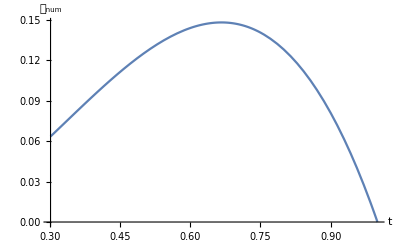

```mathematica
Plot[DangWxl[η] ,{η,ηin,ETA0},WorkingPrecision->30,AxesLabel->{"t","𝒟_num"}]
```

In EdS the angular diameter distance as function of the redshift is:

```mathematica
χz[𝓏_]:=1/(1+𝓏)^2 2/𝒽0(1+𝓏-Sqrt[1+𝓏]);
```

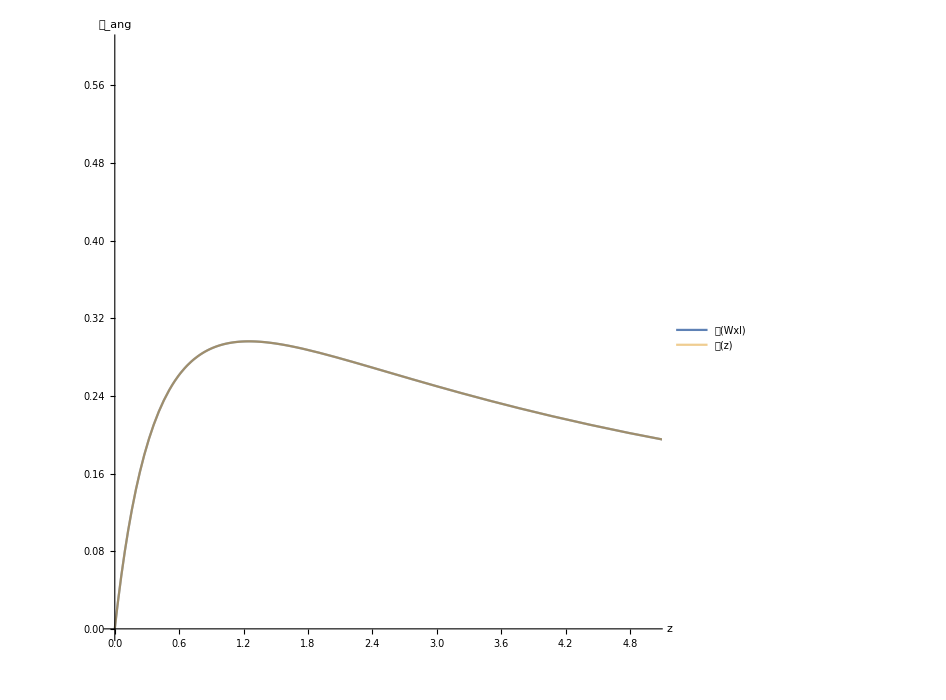

```mathematica
ParametricPlot[{{redshift[η],𝒽0 DangWxl[η]},{redshift[η],𝒽0 χz[redshift[η]]}},{η,ηin,ETA0},PlotRange->{{0,5},{0,0.6}},PlotStyle->{Thick, Opacity[0.5],Opacity[0.5]},AspectRatio->1,ImageSize->700,PlotLegends->{Style["𝒟(Wxl)",Large],Style["𝒟(z)",Large]},AxesLabel->{Style["z",Large],Style["𝒟_ang",Large]}]
```

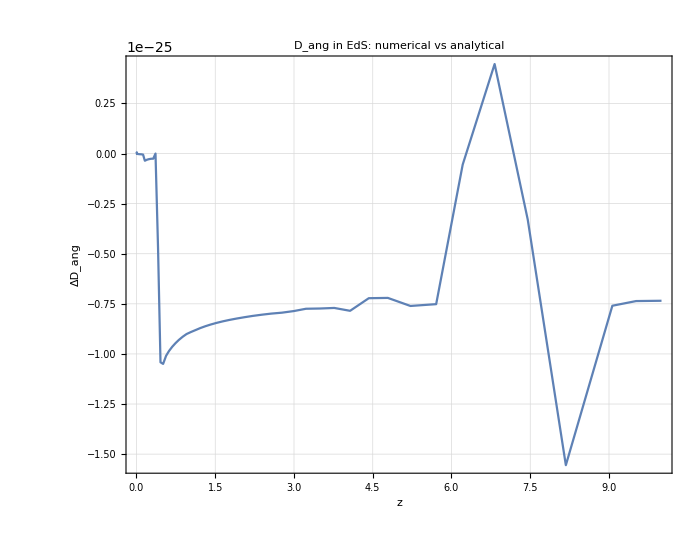

```mathematica
(*LCDMdD=*)ParametricPlot[{redshift[η],  (DangWxl[η]-χz[redshift[η]])/χz[redshift[η]]},{η,ηin,ETA0},PlotRange->All(*{{0,10},{0,2 10^-23}}*),ImageSize->700,AspectRatio->0.8,Evaluate[StandardPlotStyle[18,24,"ΔD_ang","z","D_ang in EdS: numerical vs analytical",{},{}]], WorkingPrecision->45]
```

```mathematica
dzplot=ParametricPlot[{redshift[η], Evaluate[ redshift[η]/zan[η]-1]},{η,ηin,ETA0},WorkingPrecision->40,ImageSize->700,AspectRatio->0.8,PlotRange->All,Evaluate[StandardPlotStyle[18,24,"Δz","z","Redshift in EdS: numerical vs analytical ",{},{}]]]
```

-Graphics-

### Luminosity distance, Parallax distance and the distance slip

```mathematica
(*𝒲[t_]:=𝒲2[t]*)
```

```mathematica
Timing[tmpWAA=Table[𝒲[η][[1,1]][[i,j]],{i,2,3},{j,2,3}];]
```

{0.003517,Null}

```mathematica
Timing[detWxxAB[t_]=Evaluate[Simplify[Sqrt[Abs[(Det[tmpWAA])]]]/.η->t];]
```

{0.017297,Null}

```mathematica
Dpar[η_]=Evaluate[(ldown[ETA0].u[ETA0])Evaluate[detWxlAB[η]/detWxxAB[η]]/.Join[param,totBG]];
```

```mathematica
DangWxl[ETA0]
Dpar[ETA0]
```

0.

0.

```mathematica
Dlum[t_]=(1+redshift[t])^2 DangWxl[t];
χlum[𝓏_]:=2/𝒽0(1+𝓏-Sqrt[1+𝓏]);
```

```mathematica
ParametricPlot[{{redshift[t], 𝒽0 DangWxl[t]},{redshift[t],𝒽0 Dlum[t]},{redshift[t],𝒽0 Dpar[t]}} ,{t,ηin,ETA0},WorkingPrecision->30,ImageSize->700,AspectRatio->0.8,PlotRange->{{0,10},{-0.001,3.5}},Evaluate[StandardPlotStyle[18,24,"D/D_ℋ_0","z","Distances in EdS model",{"D_ang","D_lum","D_par"},{1,0.5}]]]
```

-Graphics-

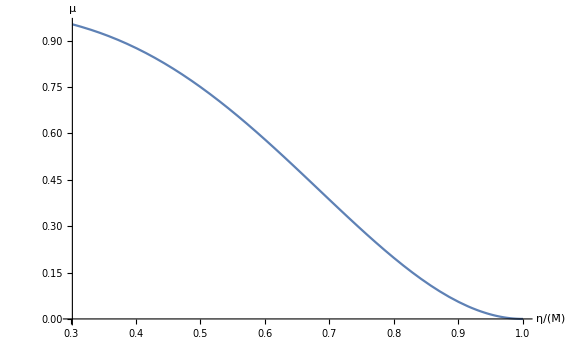

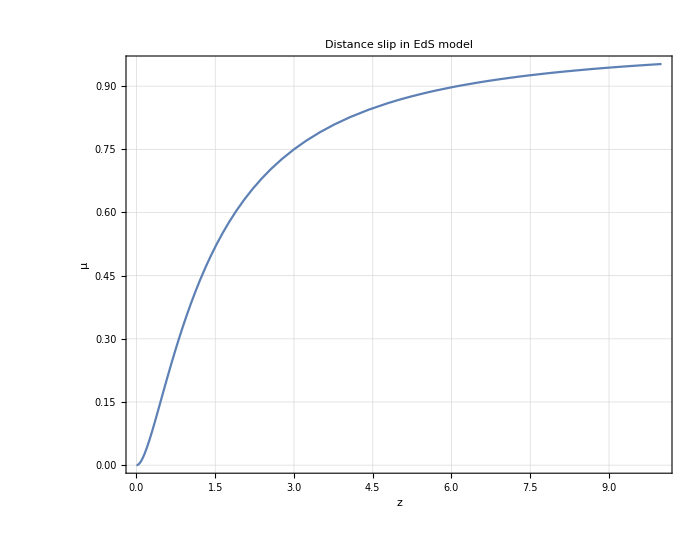

```mathematica
Plot[1-DangWxl[t]^2/Dpar[t]^2 ,{t,ηin,ETA0},WorkingPrecision->30,AxesLabel->{Style["η/(M̄)",Large],Style["μ",Large]},ImageSize->Large]
ParametricPlot[{redshift[t], 1-DangWxl[t]^2/Dpar[t]^2},{t,ηin,ETA0},WorkingPrecision->30,ImageSize->700,AspectRatio->0.8,PlotRange->All,Evaluate[StandardPlotStyle[18,24,"μ","z","Distance slip in EdS model",{ },{ }]]]
```

```mathematica
ADpar[z_]:=1/𝒽0 (Sqrt[1+z]-1)/(3/2 Sqrt[1+z]-1)
```

```mathematica
ParametricPlot[{{redshift[t],𝒽0 Dpar[t]},{redshift[t],𝒽0 ADpar[redshift[t]]}} ,{t,ηin,ETA0},WorkingPrecision->30,ImageSize->700,AspectRatio->0.8,PlotRange->All(*{{0,5},{0,1}}*),Evaluate[StandardPlotStyle[18,24,"D/D_ℋ_0","z","D_par in ΛCDM model",{"D_par^BGO","D_par^an"},{1,0.5}]]]
```

-Graphics-

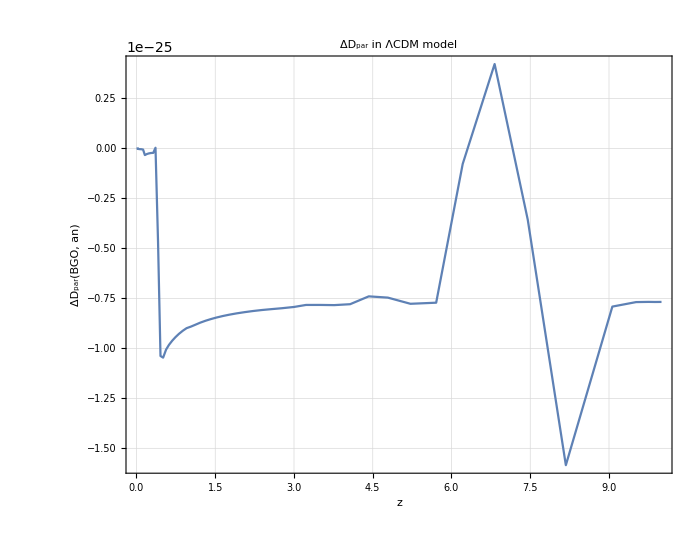

```mathematica
ParametricPlot[{redshift[t], Dpar[t]/ADpar[redshift[t]]-1},{t,ηin,ETA0},WorkingPrecision->30,ImageSize->700,AspectRatio->0.8,PlotRange->All,Evaluate[StandardPlotStyle[18,24,"ΔD_par(BGO, an)","z","ΔD_par in ΛCDM model",{ },{ }]]]
```

### Redshift Drift

```mathematica
𝒲XX[η_]:=Mxx/.functional[η];
𝒲LX[η_]:=Mlx/.functional[η];
𝒲XL[η_]:=Mxl/.functional[η];
𝒲LL[η_]:=Mll/.functional[η];
I𝒲XL[η_]:=Inverse[𝒲XL[η]];
```

```mathematica
Uoo[η_]:=-hDD.I𝒲XL[η].𝒲XX[η]
Uoe[η_]:=hDD.I𝒲XL[η]
Ueo[η_]:=-(hDD.𝒲LX[η]-hDD.𝒲LL[η].I𝒲XL[η].𝒲XX[η])
Uee[η_]:= -hDD.𝒲LL[η].I𝒲XL[η]
```

```mathematica
𝒰dd[η_]:= {{Uoo[η],Uoe[η]},{Ueo[η],Uee[η]}}
```

```mathematica
(*four acceleration can be calculated as a^ν==u^μ∇_μ u^ν*)
```

```mathematica
up={1/𝒶[η],0,0,0}(*{u0[η],u1[η],u2[η],u3[η]}*);
Table[Sum[(up[[j]]D[up[[i]],X4[[j]]]),{j,1,4}]+Sum[Christoffel[{{-(𝒶[η])^2,0,0,0},{0,(𝒶[η])^2,0,0},{0,0,(𝒶[η])^2,0},{0,0,0,(𝒶[η])^2}},X4][[i,j,s]]up[[j]]up[[s]],{j,1,4},{s,1,4}]//Simplify,{i,1,4}]
```

{0,0,0,0}

Note: the source and observer four-velocity and acceleration have to be projected in the parallel transported frame, since the BGO 𝒲 are expressed in the SNF.

```mathematica
e0[s_]=ldown[s]/Q;
e1[η_]=gg4[η].(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]])/.totBG;
e2[η_]=gg4[η].(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]])/.totBG;
e3[η_]=(gg4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]])+e0[η])/Q/.totBG;
```

```mathematica
up[η_]:={e0[η].u[η],e1[η].u[η],e2[η].u[η],e3[η].u[η]}
```

```mathematica
uE[η_]:={e0[η].u[η],e1[η].u[η],e2[η].u[η],e3[η].u[η]}
aE[η_]:={0,0,0,0}
uO[η_]:={1/A[η],0,0,0}
aO[η_]:={0,0,0,0}
```

```mathematica
ΞDoppler[η_]:=(ldown[η]/(uE[η].ldown[η])).(aE[η]/(1+redshift[η]))-(ldown[ETA0]/(uO[ETA0].ldown[ETA0])).aO[ETA0]
lnzdrift[η_]:=(ΞDoppler[η]-1/(uO[ETA0].ldown[ETA0])(Uoo[η].uO[ETA0].uO[ETA0]+1/(1+redshift[η])Uoe[η].uO[ETA0].uE[η]+1/(1+redshift[η])Ueo[η].uE[η].uO[ETA0]+1/(1+redshift[η])^2 Uee[η].uE[η].uE[η]))/.BGO/.geodesic
```

Dimensions: we want to give physical units to our dimensionless redshift drift. To do so, we need to convert L in the unit we want to use, i.e. in 1/s, using c and G.
							s^-1=(Mpc/s)/Mpc=[c/L]=(299792458 3.24078 10^-23)/L

```mathematica
cL=(299792458 3.24078 10^-23)/L(*c/L==(Mpc/s)/Mpc=1/s*)
```

1.091494704×10^-18

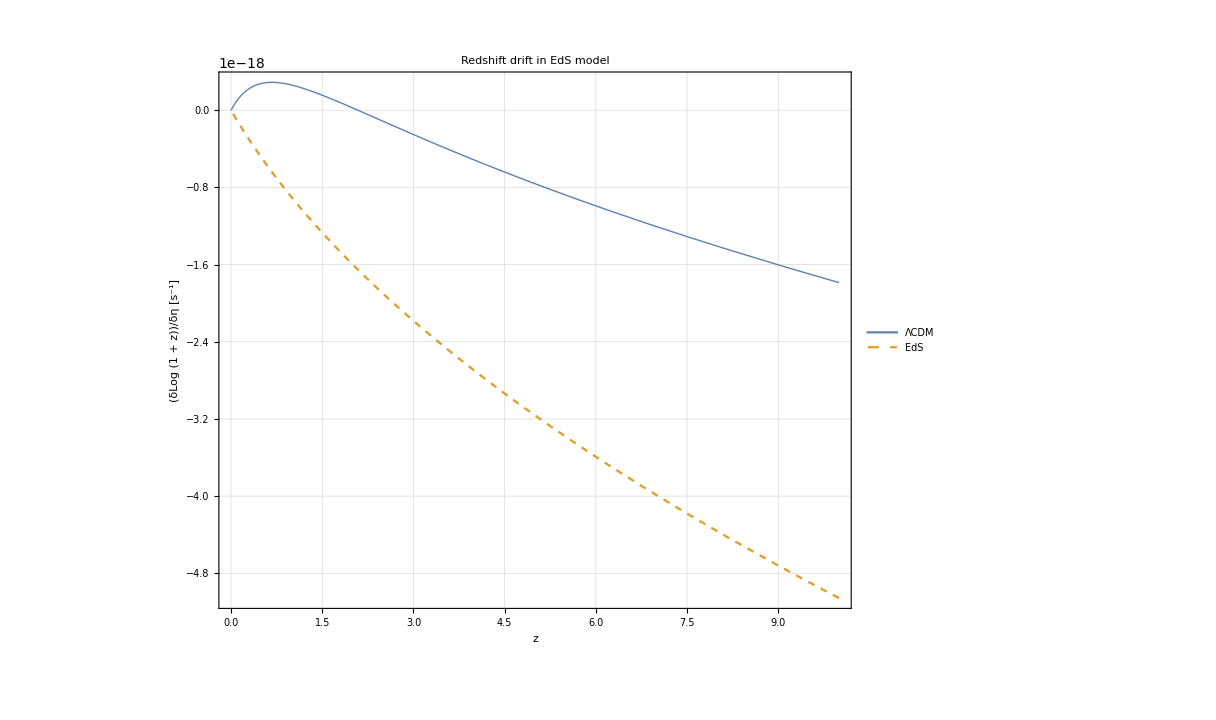

```mathematica
ParametricPlot[{{redshift[t],cL 𝒽0/(1+redshift[t])((1+redshift[t])-Sqrt[0.3(1+redshift[t])^3+0.7])/.param},{redshift[t],cL lnzdrift[t]}},{t,ηin,ETA0},ImageSize->900,PlotRange->All,AspectRatio->0.8,PlotStyle->{Thick,Dashed},Evaluate[StandardPlotStyle[20,24,"(δLog (1 + z))/δη [s^-1]","z","Redshift drift in EdS model",{"ΛCDM","EdS" },{0.8,0.8 }]]]
```

```mathematica
δzAN[η_]:=𝒽0(1-Sqrt[1+redshift[η]])
```

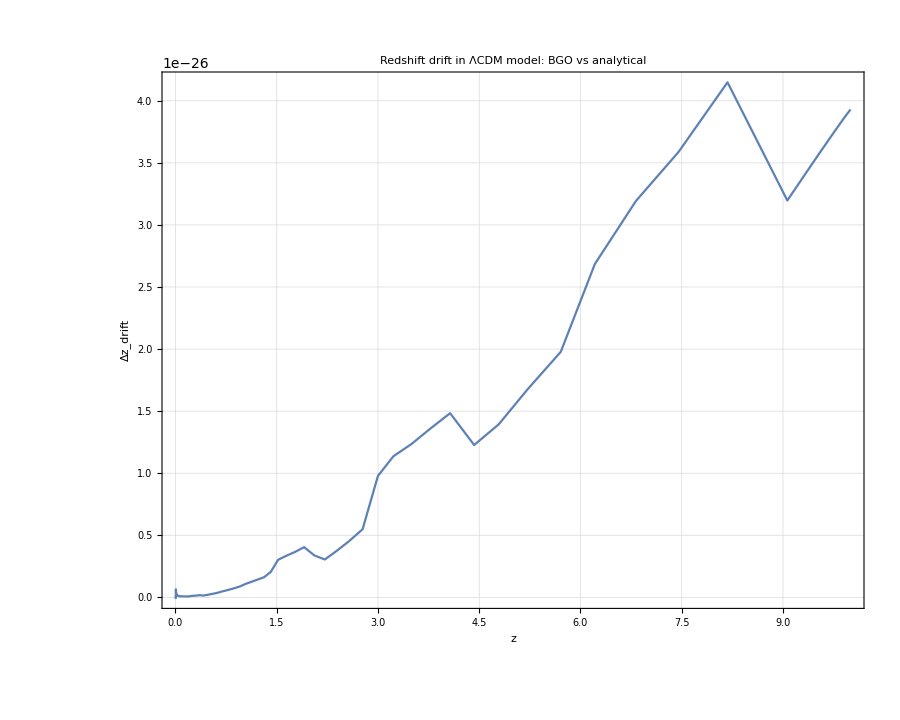

```mathematica
ParametricPlot[{redshift[t],lnzdrift[t]/δzAN[t]-1},{t,ηin,ETA0},ImageSize->900,PlotRange->All,AspectRatio->0.8,WorkingPrecision->60,Evaluate[StandardPlotStyle[20,24,"Δz_drift","z","Redshift drift in EdS model: BGO vs analytical",{},{}]]]
```

The observables are saved as output

```mathematica
{zEdS->(Evaluate[redshift[#]]&),DangEdS->(Evaluate[DangWxl[#]]&) ,DlumEdS->(Evaluate[Dlum[#]]&) , DparEdS->(Evaluate[Dpar[#]]&) , ZdriftEdS->(Evaluate[lnzdrift[#]]&) }>>"observables_EdS_bisect.m"
```

```mathematica
geodesic>>"EdS_geodesic_bisect.m"
totBG>>"EdS_ptSNF_bisect.m"
BGO>>"EdS_BGO_bisect.m"
```

### Shear and expansion

```mathematica
Timing[tmpWllAB=SetPrecision[Table[𝒲[η][[2,2]][[i,j]],{i,2,3},{j,2,3}],50];]
IWxlAB=Inverse[tmpWAB];
```

{0.003806,Null}

```mathematica
trxlll[t_]=SetPrecision[Evaluate[Tr[IWxlAB.tmpWllAB]/.η->t],50];
```

```mathematica
DDang[t_]=1/2 DangWxl[t] trxlll[t];
```

```mathematica
𝒮[t_]=Evaluate[(tmpWllAB.IWxlAB)//.η->t];
```

```mathematica
expansion[η_]=Tr[𝒮[η]]/2;
shear[η_]=Sqrt[(Tr[𝒮[η].𝒮[η]]/2-(Tr[𝒮[η]]/2)^2)];
```

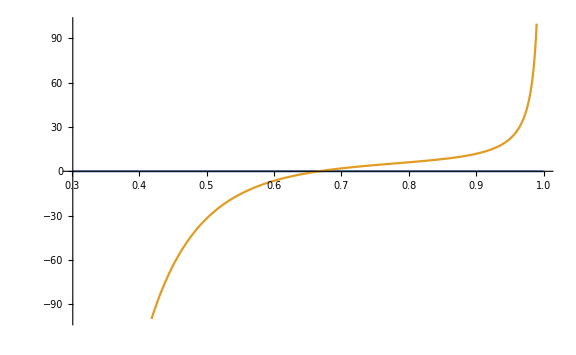

```mathematica
Plot[{shear[η],expansion[η]},{η,ηin,ETA0},ImageSize->Large,PlotRange->100]
```

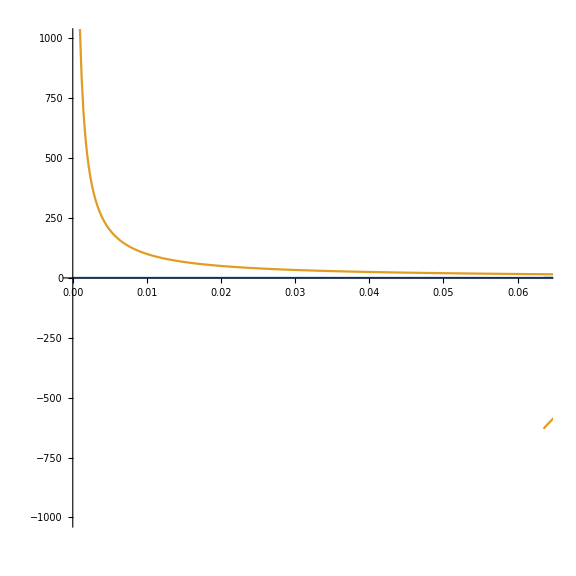

```mathematica
ParametricPlot[{{DangWxl[η], shear[η]},{DangWxl[η],expansion[η]}},{η,ηin,ETA0},ImageSize->Large,PlotRange->{{DangWxl[ETA0], DangWxl[ηin]},{-1000,1000}},AspectRatio->1]
```

#### Deviation (to be fixed)

```mathematica
δx={0,0,-10^-6/8,-10^-6/8};
δXf[t_]=𝒲[t][[1,2]].δx;
```

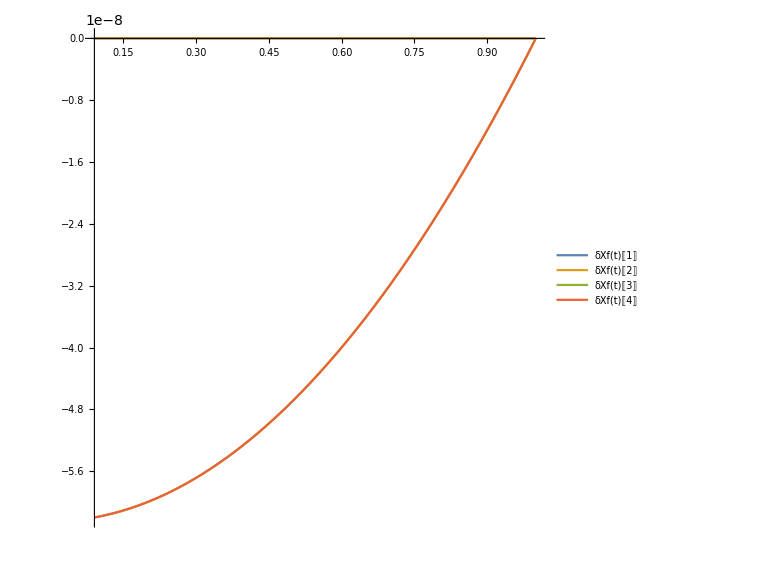

```mathematica
Plot[{δXf[t][[1]],δXf[t][[2]],δXf[t][[3]],δXf[t][[4]]},{t,tin,t0},ImageSize->Large,AspectRatio->1,PlotLegends->"Expressions"]
```

```mathematica
δX0[t_]=(F0[t]/αα[t]).δXf[t]/.Join[param,totBG];
δX1[t_]=(F[t][[1]]-F0[t](ββ[t][[1]])/αα[t]).δXf[t]/.Join[param,totBG];
δX2[t_]=(F[t][[2]]-F0[t](ββ[t][[2]])/αα[t]).δXf[t]/.Join[param,totBG];
δX3[t_]=(F[t][[3]]-F0[t](ββ[t][[3]])/αα[t]).δXf[t]/.Join[param,totBG];
```

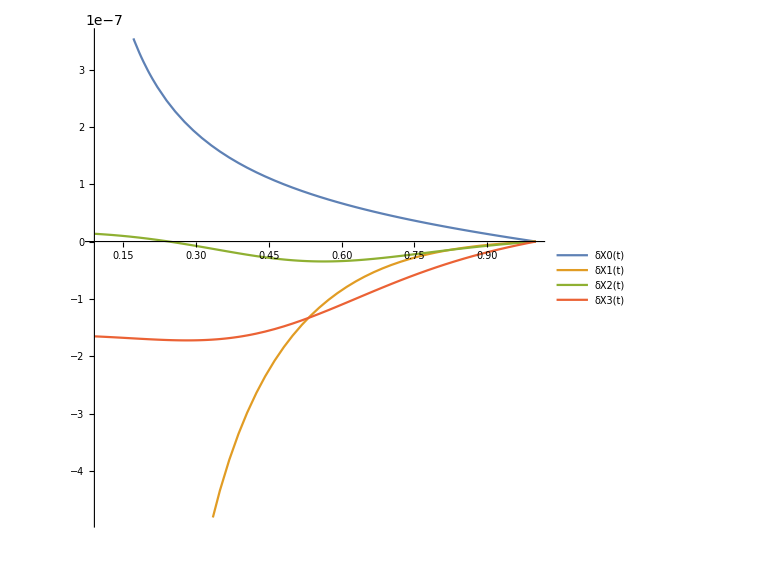

```mathematica
Plot[{δX0[t],δX1[t],δX2[t],δX3[t]},{t,tin,t0},ImageSize->Large,AspectRatio->1,PlotLegends->"Expressions"]
```

```mathematica
Δx[t_]=-{δX0[t],δX1[t],δX2[t],δX3[t]}.ndown[t]/.Join[param,totBG];
ξ[t_]=({δX0[t],δX1[t],δX2[t],δX3[t]}-Δx[t]nup[t])/.Join[param,totBG];
```

```mathematica
Δx[tin]
ξ[tin]
```

6.818181818181818181818181819046368504282004830124×10^-7

{0,-7.498367347439063605211069230335548086433033267092×10^-6,1.35376494916261527108299750093227530173135479025×10^-8,-1.653638872474773213994219687305054196172348585874×10^-7}

```mathematica
δXc[t_]={ξ[t][[2]],ξ[t][[3]],ξ[t][[4]]};
trajectory[t_]=Evaluate[{x[t],y[t],z[t]}/.totBG];
Show[ParametricPlot3D[trajectory[η],{η,tin,t0},PlotRange->{{-1,1},{-1,1},{-1,1}}](*/.Line[x_]:>Sequence[Arrowheads[Table[.02,{100/10}]],Arrow@Line[x]]*) ,Table[Graphics3D[{(*{Opacity[η/300+0.28],Black,Arrowheads[0.02],Arrow[{trajectory[η],(trajectory[η]+40(Pu[η]/.totBG))}]},{Opacity[η/300+0.28],Green,Arrowheads[0.02],Arrow[{trajectory[η],(trajectory[η]+40(P1[η]/.totBG))}]},{Opacity[η/300+0.28],Blue,Arrowheads[0.02],Arrow[{trajectory[η],(trajectory[η]+40(P2[η]/.totBG))}]},{*)(*Opacity[η/300+0.28],*)Red,Arrowheads[0.01],Arrow[{trajectory[η],(trajectory[η]+1/10(δXc[η]/.totBG))}]}],{η,ηin,ETA0,(ETA0-ηin)/30}] , ImageSize->700,AxesLabel->{Style["x/(M̄)",Large],Style["y/(M̄)",Large],Style["z/(M̄)",Large]},AxesStyle->Directive[Black,12],Boxed->False,ViewPoint->{0,100,10}]
```

-Graphics3D-